```mathematica
(*Quit[]*)
```

```mathematica
<<RandFile`
```

Package RandFile version 0.1.4 (last modification: 14/11/2018).

Usage notes:

1) Almost all provided functions require to set a global variable pointing to file with random data! This can be done by using SetTrueRandomDataFile function. For example SetTrueRandomDataFile["/home/user_name/data/sample_file.bin"] for GNU/Linux systems or SetTrueRandomDataFile["/Users/user_name/data/sample_file.bin"] for OS X systems. Please mind that it is advised to use this function only once during the session.

2) If you intend to use TrueRandomSequence function you must use SetMaxTrueRandomSequenceLength and declare at least one sequence. Currently declared sequences can be displayed by calling GetTrueRandomDataMarkers[]. Once defined, the used maximal length cannot be changed during the session.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/RandFile/examples

```mathematica
TrueRandomPi[dataFile_String]:=With[{samplePoints=5000},
SetTrueRandomDataFile[dataFile];
data=Table[TrueRandomReal[{0,1}],{i,samplePoints},{j,2}];
CloseTrueRandomDataFile[];
dataCircle=Select[data,(1/2-#[[1]])^2+(1/2-#[[2]])^2≤1/4&];
complement=Complement[data,dataCircle];
If[Length[complement]==0,complement={{1,1}}];
4*Length[dataCircle]/samplePoints
];
```

```mathematica
α[7]=2/10;
α[k_]:=Module[{i},Sum[1/2^(i-1),{i,1,k-1}]/10];
```

```mathematica
entropyTheory[k_]:=Module[{p1},
p1=(0.3+α[k]);
-Log[2,p1] p1 - Log[2,1-p1](1-p1)
]
```

```mathematica
(* this was calculated during the sample generation in RandFile_FileGenerator.nb *)
tabQuality=Map[Flatten,{{{0.699105,0.882383}},{{0.600255,0.970801}},{{0.549744,0.992848}},{{0.524911,0.998209}},{{0.513581,0.999468}},{{0.506958,0.99986}},{{0.500608,0.999999}}}]
```

{{0.699105,0.882383},{0.600255,0.970801},{0.549744,0.992848},{0.524911,0.998209},{0.513581,0.999468},{0.506958,0.99986},{0.500608,0.999999}}

```mathematica
tabEntReal=tabQualityᵀ[[2]]
```

{0.882383,0.970801,0.992848,0.998209,0.999468,0.99986,0.999999}

```mathematica
tabPi=Table[TrueRandomPi["piSample"<>ToString[i]<>".bin"]//N,{i,1,7}]
```

Using file "piSample1.bin" which contains 80000 bytes of data.

Using file "piSample2.bin" which contains 80000 bytes of data.

Using file "piSample3.bin" which contains 80000 bytes of data.

Using file "piSample4.bin" which contains 80000 bytes of data.

Using file "piSample5.bin" which contains 80000 bytes of data.

Using file "piSample6.bin" which contains 80000 bytes of data.

Using file "piSample7.bin" which contains 80000 bytes of data.

{2.4168,2.9792,3.0864,3.112,3.156,3.1384,3.1416}

```mathematica
tabPiPlot=tabPi[[1;;7]];
tabEntRealPlot=tabEntReal[[1;;7]];
tabPiInset=tabPi[[3;;7]];
tabEntRealInset=tabEntReal[[3;;7]];
```

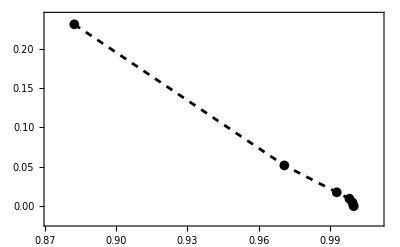

```mathematica
plotRelativeErrPIvsEntropy=ListPlot[
{tabEntRealPlot,Abs[tabPiPlot-π]/π}ᵀ,
PlotRange->{{Min[tabEntRealPlot]-0.01,Max[tabEntRealPlot]+0.01},{Min[Abs[tabPiPlot-π]/π]-0.02,Max[Abs[tabPiPlot-π]/π]+0.01}},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
Joined->True,
Frame->True,
PlotMarkers->{Automatic,10},
PlotStyle->{Directive[Black,Dashed,Thickness[0.005]]}
]
```

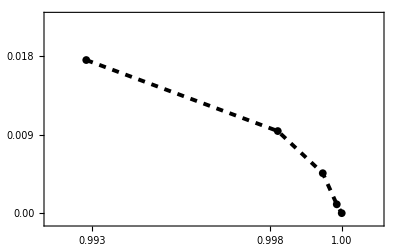

```mathematica
plotRelativeErrPIvsEntropyInset=ListPlot[
{tabEntRealInset,Abs[tabPiInset-π]/π}ᵀ,
FrameStyle->Directive[8],
PlotRange->{{Min[tabEntRealInset]-0.001,Max[tabEntRealInset]+0.001},{-0.001,Max[Abs[tabPiInset-π]/π]+0.005}},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
Joined->True,
Frame->True,
PlotMarkers->{Automatic,8},
PlotStyle->{Directive[Black,Dashed,Thickness[0.007]]},
FrameTicks->{{{{0.000,"0.00"},0.009,0.018},Automatic},{{0.993,0.998,{1.00,"1.00"}},Automatic}}
]
```

```mathematica
plotRelativeErrPIvsEntropyWithInset=Graphics[
{
First[plotRelativeErrPIvsEntropy],
Inset[plotRelativeErrPIvsEntropyInset,{0.967,0.175},Automatic,Scaled[.5]]
},
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
AspectRatio->1/GoldenRatio,
FrameLabel->{"entropy","relative error"},
Frame->True
]
```

-Graphics-

```mathematica
Export["plotEntropyPiErr.pdf",plotRelativeErrPIvsEntropyWithInset]
```

plotEntropyPiErr.pdf

Samples in the square

```mathematica
(*CloseTrueRandomDataFile[]*)
```

```mathematica
TrueRandomPiIlustrated[dataFile_String]:=Module[{a=5000,c=1,b=3,j,data,p1,p2,p3,app},
SetTrueRandomDataFile[dataFile];
data=Table[TrueRandomReal[{0,1}],{i,a},{j,2}];
CloseTrueRandomDataFile[];

dataCircle=Select[data,(0.5-#[[1]])^2+(0.5-#[[2]])^2≤(0.5)^2&];
complement=Complement[data,dataCircle];If[Length[complement]==0,complement={{1,1}}];

p1=Graphics[{Black,PointSize[0.005],Point[dataCircle]},Background->Green];
p2=Graphics[{Blue,PointSize[0.005],Point[complement]},Background->White];
p3=Graphics[{Circle[{1/2,1/2},1/2],EdgeForm[Thin],Opacity[0],Rectangle[{0,0},{1,1}]}];
app=4*Length[dataCircle]/a;
(*Column[{
Rasterize[Show[p2,p1,ImageSize->{350,350}]],
Text@Style[Row[{"π ≈ ",N[app,6]}],20]
},
Center]*)
Rasterize[Show[p2,p1,p3,ImageSize->{350,350}]]
];
```

```mathematica
Table[plotHitsSample[i]=TrueRandomPiIlustrated["piSample"<>ToString[i]<>".bin"],{i,Range[7]}]
```

Using file "piSample1.bin" which contains 80000 bytes of data.

Using file "piSample2.bin" which contains 80000 bytes of data.

Using file "piSample3.bin" which contains 80000 bytes of data.

Using file "piSample4.bin" which contains 80000 bytes of data.

Using file "piSample5.bin" which contains 80000 bytes of data.

Using file "piSample6.bin" which contains 80000 bytes of data.

Using file "piSample7.bin" which contains 80000 bytes of data.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Export["plotHitsSample"<>ToString[#]<>".pdf",plotHitsSample[#]]&,Range[7]]
```

{plotHitsSample1.pdf,plotHitsSample2.pdf,plotHitsSample3.pdf,plotHitsSample4.pdf,plotHitsSample5.pdf,plotHitsSample6.pdf,plotHitsSample7.pdf}